```mathematica
(*Lets assume that travel time is normally distrubted. --> Or at least that median and mean are equal*)
```

```mathematica
datamob=Abs[RandomVariate[NormalDistribution[60,15],1000]]; (*Only allow postive travel times --> not truly normal anymore, truncated*)
```

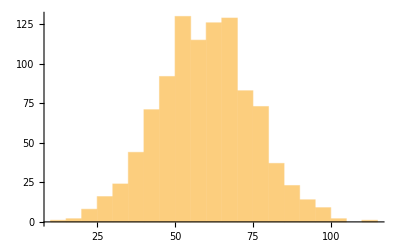

59.6931

59.8129

```mathematica
Histogram[datamob]
Mean[datamob]
Median[datamob]
```

```mathematica
Intervention 1:
```

```mathematica
i=1;
datamobIntervened=List[];
While[i≤Length[datamob],
inter=Abs[datamob[[i]]+RandomChoice[{-5,5}]](*intervention*);
AppendTo[datamobIntervened,inter];
i++;
]
datamobIntervened=Flatten[datamobIntervened];
```

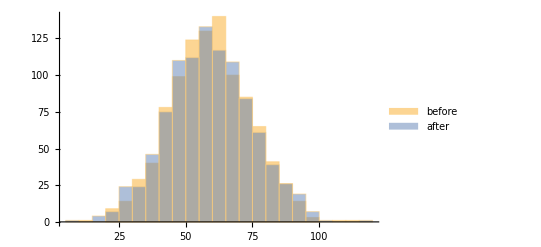

58.9562

58.4486

```mathematica
Histogram[{datamob,datamobIntervened},ChartLegends->{before,after}]
Mean[datamobIntervened]
Median[datamobIntervened]
```

```mathematica
Improvement on average
```

```mathematica
PercentForm[Log[Mean[datamob]/Mean[datamobIntervened]]]
```

-5.444%

```mathematica
Democratic Improvement
```

```mathematica
ListProduct[x_List]:=Times@@x
```

```mathematica
PercentForm[Mean[Log[datamob/datamobIntervened]]]
```

-2.009%

```mathematica
GeometricMean[datamob]/GeometricMean[datamobIntervened]-1
```

0.0014381

```mathematica
(*Loop*)
differencemedian=List[];
differencemedianT=List[];
For[j=1,j≤200,
datamob=Abs[RandomVariate[NormalDistribution[60,15],1000]];
i=1;
datamobIntervened=List[];
While[i≤Length[datamob],
inter=Abs[datamob[[i]]+1.1](*Abs[datamob[[i]]+RandomChoice[{-5,2}]]*)(*intervention*);
AppendTo[datamobIntervened,inter];
i++;
];
datamobIntervened=Flatten[datamobIntervened];
verschil1=(Log[Mean[datamob]/Mean[datamobIntervened]])-(Log[Median[datamob]/Median[datamobIntervened]]);
verschil2=Mean[Log[datamob/datamobIntervened]]-(Log[Median[datamob]/Median[datamobIntervened]]);
AppendTo[differencemedian,verschil1];
AppendTo[differencemedianT,verschil2];
j++;
]
```

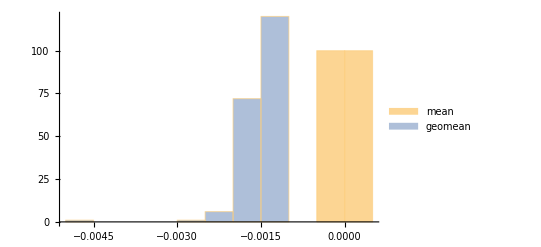

```mathematica
Histogram[{differencemedian,differencemedianT},ChartLegends->{"mean","geomean"}]
```

```mathematica
Mean[differencemedian^2] (*No clear winner*)
```

9.93575×10^-9

```mathematica
Mean[differencemedianT^2]
```

2.35469×10^-6

```mathematica
Intervention 2:
```

```mathematica
differencemedian=List[];
differencemedianT=List[];
datamob=Abs[RandomVariate[NormalDistribution[60,15],1000]];
datamobIntervened=datamob;
For[j=1,j≤100,
ri=RandomInteger[{1,1000},20];
datamobIntervened[[ri[[1;;10]]]]=If[j==1,Abs[datamob[[ri[[1;;10]]]]*1.33],Abs[datamobIntervened[[ri[[1;;10]]]]*1.33]];
(*datamobIntervened[[ri[[11;;20]]]]=Abs[datamob[[ri[[11;;20]]]]+33]*); (*intervention*)
verschil1=(Log[Mean[datamob]/Mean[datamobIntervened]])-(Log[Median[datamob]/Median[datamobIntervened]]);
verschil2=Mean[Log[datamob/datamobIntervened]]-(Log[Median[datamob]/Median[datamobIntervened]]);
AppendTo[differencemedian,verschil1];
AppendTo[differencemedianT,verschil2];
j++;
]
```

```mathematica
Improvement on average
```

```mathematica
Mean[datamob]/Mean[datamobIntervened]
```

0.718376

```mathematica
Log[Mean[datamob]/Mean[datamobIntervened]]
```

-0.330762

```mathematica
PercentForm[Log[Mean[datamob]/Mean[datamobIntervened]]]
```

-33.08%

```mathematica
Democratic Improvement
```

```mathematica
ListProduct[x_List]:=Times@@x
```

```mathematica
PercentForm[Mean[Log[datamob/datamobIntervened]]]
```

-28.46%

```mathematica
GeometricMean[datamob]/GeometricMean[datamobIntervened]-1
```

-0.247691

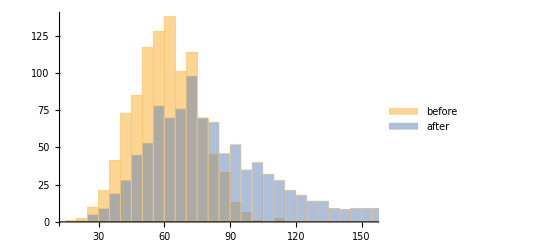

60.9427

84.8339

```mathematica
Histogram[{datamob,datamobIntervened},ChartLegends->{before,after}]
Mean[datamob]
Mean[datamobIntervened]
```

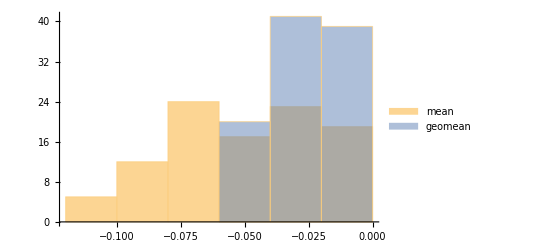

```mathematica
Histogram[{differencemedian,differencemedianT},ChartLegends->{"mean","geomean"}]
```

```mathematica
doesn't show anything because we keep adding begiining too when to predictions are still quite good
```

```mathematica
Mean[differencemedian^2] (*No clear winner*)
```

0.00344689

```mathematica
Mean[differencemedianT^2]
```

0.000982107

```mathematica
main problem is that i need to define it the other way around! so that going down is bad and going up is good on your axis
grotere impact
```

```mathematica
(*MAybe a uniform distribution is a better starting point to understand what is going on?*)
```

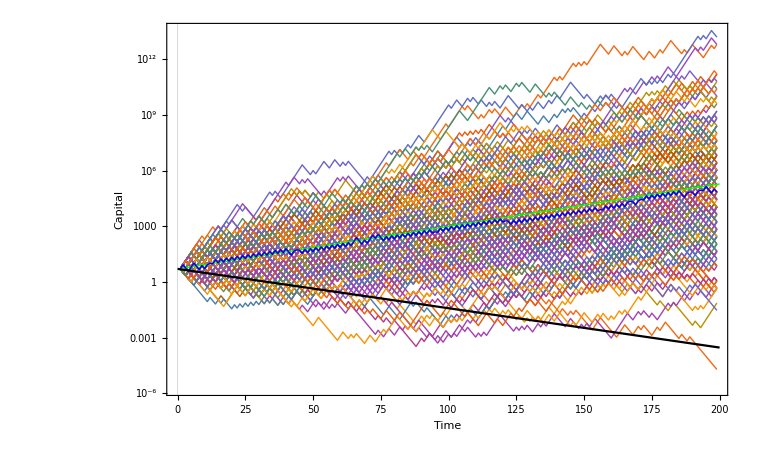

```mathematica
n=1;f=List[];
While[n≤200,
l=List[];
t=1;
 k= 5;
While[t<200,
AppendTo[l,k] ;
a= RandomInteger[{1,2}];
k= If[a==1, (k*(1/1.5)), (k*(1/0.6))];
t++;
];
AppendTo[f,l];
n++;
];
tickSpecification=Table[i,{i,-100,100}];
p1=ListLinePlot[f,ScalingFunctions->"Log", Ticks -> {Automatic, N[tickSpecification,1]},PlotTheme->"Scientific",PlotStyle->Directive[Thin],FrameLabel->{"Time","Capital"}];
p2=ListLinePlot [Table[Log[10],t],PlotStyle->Directive[Red,Thick]];
p3 =ListLinePlot[Log[Median[f]], PlotStyle->Directive[Blue,Thick]];
p4=ListLinePlot[Log[Mean[f]], PlotStyle->Directive[Green,Thick]];
v=Plot[Log[5]+Log[1/Sqrt[1.5* 0.6]]*x,{x,0,t},PlotStyle->Directive[Green,Thick]];
expect = Plot[Log[5*(1/1.05)^x],{x,0,t},PlotStyle->Directive[Black],Ticks -> {Automatic, N[tickSpecification,1]}];
multibet=Show[p1,v,p3,(*(*p2,*)p3,p4,v,*)expect(*,AxesLabel->{HoldForm[T],HoldForm[Ln C]}*)]
```

```mathematica
N[Sqrt[101]]
```

10.0499

```mathematica
N[(101+100)/20]
```

10.05